```mathematica
jac[v_]:=v/(x+y-v)
```

```mathematica
D[jac[v],v]^2//FullSimplify
```

(x+y)^2/(-v+x+y)^4

```mathematica
Clear[j]
```

```mathematica
(x+y)^2/(-v+x+y)^4/(1/(y(x-v))+1/(v(y-v)))/.v->j/(1+j)(x+y)//FullSimplify
```

-(j (1+j)^3 (j x-y) y (-x+j y))/((x+y) (-x y-2 j x y+j^2 (x^2+x y+y^2)))

```mathematica
-(j (1+j)^3 (j x-y) y (-x+j y))/((x+y) (-x y-2 j x y+j^2 (x^2+x y+y^2)))/.y->c x
```

```mathematica
-(j (1+j)^3 (j x-y) y (-x+j y))/((x+y) (-x y-2 j x y+j^2 (x^2+x y+y^2)))==(j (1+j)^3 y(y-j x) (x-j y))/((x+y) (x y+2 j x y-j^2 (x^2+x y+y^2)))//FullSimplify
```

True

```mathematica
Limit[-(c j (1+j)^3 x (-c x+j x) (-x+c j x))/((x+c x) (-c x^2-2 c j x^2+j^2 (x^2+c x^2+c^2 x^2))),x->Infinity]
```

(c j (1+j)^3 (j+c^2 j-c (1+j^2)))/((1+c) (j^2+c^2 j^2+c (-1-2 j+j^2)))

```mathematica
(c j (1+j)^3 (j+c^2 j-c (1+j^2)))/((1+c) (j^2+c^2 j^2+c (-1-2 j+j^2)))/.c->1/c//FullSimplify
```

```mathematica
((c-j) j (1+j)^3 (-1+c j))/((1+c) (-c-2 c j+(1+c+c^2) j^2))/((c j (1+j)^3 (j+c^2 j-c (1+j^2)))/((1+c) (j^2+c^2 j^2+c (-1-2 j+j^2))))//FullSimplify
```

1/c

```mathematica
Manipulate[Plot[(c j (1+j)^3 (j+c^2 j-c (1+j^2)))/((1+c) (j^2+c^2 j^2+c (-1-2 j+j^2))),{c,j,1/j}],{{j,.1},0,1}]
```

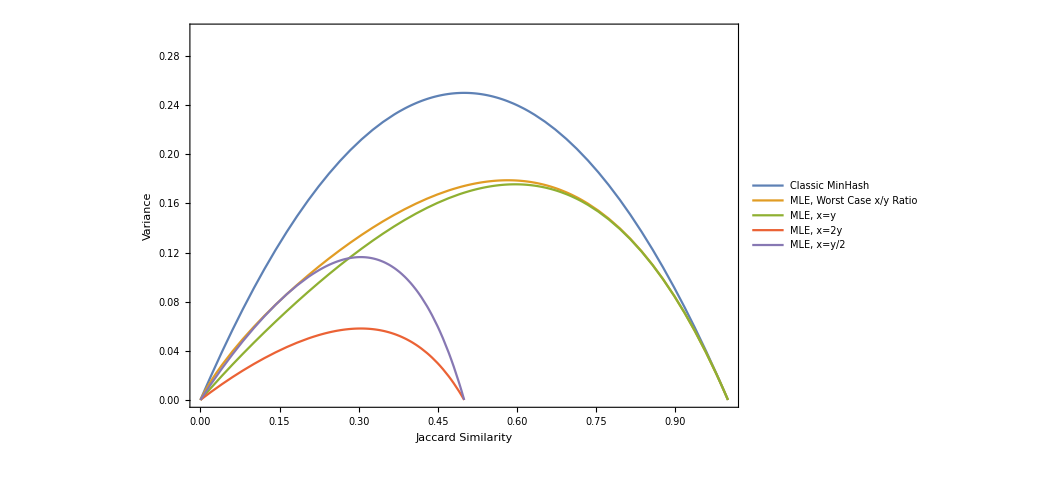

```mathematica
Plot[{j(1-j),-Root[j^6+7 j^7+20 j^8+28 j^9+14 j^10-14 j^11-28 j^12-20 j^13-7 j^14-j^15+(-2 j^4-6 j^5+10 j^6+70 j^7+126 j^8+98 j^9+14 j^10-30 j^11-20 j^12-4 j^13) #1+(j^2+j^3-12 j^4-18 j^5+33 j^6+93 j^7+74 j^8+20 j^9) #1^2+(2 j+10 j^2+18 j^3+14 j^4+4 j^5) #1^3+(1+3 j) #1^4&,2],-((-1+j) j (1+j)^3)/(2+6 j),-((-2+j) j (1+j)^3 (-1+2 j))/(-6+3 j (-4+7 j)),-(2 (-2+j) j (1+j)^3 (-1+2 j))/(-6+3 j (-4+7 j))},{j,0,1},
Axes->False,PlotLegends->Placed[{"Classic MinHash","MLE, Worst Case x/y Ratio", "MLE, x=y", "MLE, x=2y", "MLE, x=y/2"},{0.68,.2}],
Frame->{{True,False},{True,False}},
FrameLabel->{{"Variance",None},{"Jaccard Similarity",None}},PlotRange->{0,.3}]
```

```mathematica
(c j (1+j)^3 (j+c^2 j-c (1+j^2)))/((1+c) (j^2+c^2 j^2+c (-1-2 j+j^2)))/.c->1//FullSimplify
```

-((-1+j) j (1+j)^3)/(2+6 j)

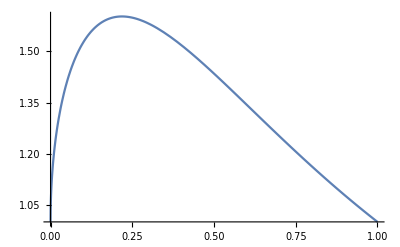

```mathematica
Plot[{j(1-j)/(-Root[j^6+7 j^7+20 j^8+28 j^9+14 j^10-14 j^11-28 j^12-20 j^13-7 j^14-j^15+(-2 j^4-6 j^5+10 j^6+70 j^7+126 j^8+98 j^9+14 j^10-30 j^11-20 j^12-4 j^13) #1+(j^2+j^3-12 j^4-18 j^5+33 j^6+93 j^7+74 j^8+20 j^9) #1^2+(2 j+10 j^2+18 j^3+14 j^4+4 j^5) #1^3+(1+3 j) #1^4&,2])},{j,0,1}
]
```

```mathematica
FindMinimum[{(-Root[j^6+7 j^7+20 j^8+28 j^9+14 j^10-14 j^11-28 j^12-20 j^13-7 j^14-j^15+(-2 j^4-6 j^5+10 j^6+70 j^7+126 j^8+98 j^9+14 j^10-30 j^11-20 j^12-4 j^13) #1+(j^2+j^3-12 j^4-18 j^5+33 j^6+93 j^7+74 j^8+20 j^9) #1^2+(2 j+10 j^2+18 j^3+14 j^4+4 j^5) #1^3+(1+3 j) #1^4&,2])/(j(1-j)),0<j<1},j]
```

{0.624003,{j→0.21845}}